## ^183Au - Positive Parity

```mathematica
x1n=Table[N[i],{i,19/2,51/2,2}];
y1n={1056,1488,1987,2540,3148,3796,4457,5133,5912};
t1n=Table[{x1n[[i]],y1n[[i]]},{i,1,Length[x1n]}];
```

```mathematica
x2n=Table[N[i],{i,9/2,53/2,2}];
y2n=Reverse[{6242,5497,4760,4050,3358,2690,2063,1492,990,566,232,12.78}];
t2n=Table[{x2n[[i]],y2n[[i]]},{i,1,Length[x2n]}];
```

```mathematica
Do[Print[t1n[[i]]],{i,1,Length[t1n]}]
```

{9.5,1056}

{11.5,1488}

{13.5,1987}

{15.5,2540}

{17.5,3148}

{19.5,3796}

{21.5,4457}

{23.5,5133}

{25.5,5912}

```mathematica
Do[Print[t2n[[i]]],{i,1,Length[t2n]}]
```

{4.5,12.78}

{6.5,232}

{8.5,566}

{10.5,990}

{12.5,1492}

{14.5,2063}

{16.5,2690}

{18.5,3358}

{20.5,4050}

{22.5,4760}

{24.5,5497}

{26.5,6242}

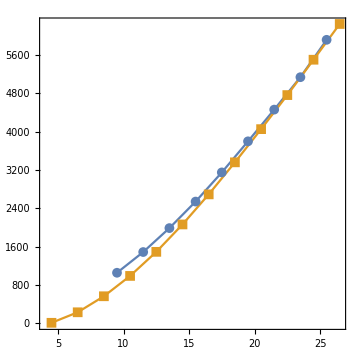

```mathematica
ListPlot[{t1n,t2n},Joined->True,PlotMarkers->{Automatic, Medium},ImageSize->Medium,Frame->True,Axes->False,AspectRatio->1]
```

## ^183Au - Positive Parity

```mathematica
x1p=Table[N[i],{i,13/2,65/2,2}];
y1p=Reverse[{7848,7103,6375,5677,4986,4308,3655,3049,2492,1983,1530,1151,867,702}];
t1p=Table[{x1p[[i]],y1p[[i]]},{i,1,Length[x1p]}];
```

```mathematica
x2p=Table[N[i],{i,23/2,43/2,2}];
y2p=Reverse[{4464,3840,3243,2684,2178,1739}];
t2p=Table[{x2p[[i]],y2p[[i]]},{i,1,Length[x2p]}];
```

```mathematica
Do[Print[t1p[[i]]],{i,1,Length[t1p]}]
```

{6.5,702}

{8.5,867}

{10.5,1151}

{12.5,1530}

{14.5,1983}

{16.5,2492}

{18.5,3049}

{20.5,3655}

{22.5,4308}

{24.5,4986}

{26.5,5677}

{28.5,6375}

{30.5,7103}

{32.5,7848}

```mathematica
Do[Print[t2p[[i]]],{i,1,Length[t2p]}]
```

{11.5,1739}

{13.5,2178}

{15.5,2684}

{17.5,3243}

{19.5,3840}

{21.5,4464}

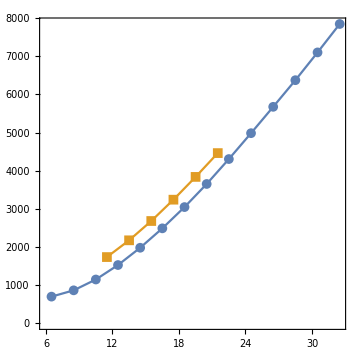

```mathematica
ListPlot[{t1p,t2p},Joined->True,PlotMarkers->{Automatic, Medium},ImageSize->Medium,Frame->True,Axes->False,AspectRatio->1]
```